Visualizing exercise acceleration data

The rows are all CSV rows, which are x, y, z, label, ...; we want just the first three, which are acceleration in 10ms^-2

```mathematica
(*fn = FileNameJoin[{NotebookDirectory[], files[[fileNumber]]}];*)
fn="~/Tmp/x.csv";
rows = Import[fn];
rowCount = Length[rows];
```

The file contains a lot of rows, so we want to select just a subset of about 20k samples

```mathematica
rowsSubset=rows[[800000;;820000,All]];
acceleration=Transpose[rowsSubset[[All,1;;3]]];
acceleration=Map[MovingAverage[#,200]&,acceleration];
normalize=Function[x,x/2000];
acceleration=normalize/@ acceleration;
labelFunction[x_]:=If[x=="exercising",-1,1];
labels=Map[labelFunction,rowsSubset[[All,4]]];
acceleration=Append[acceleration, labels];
```

Finally, we display the data

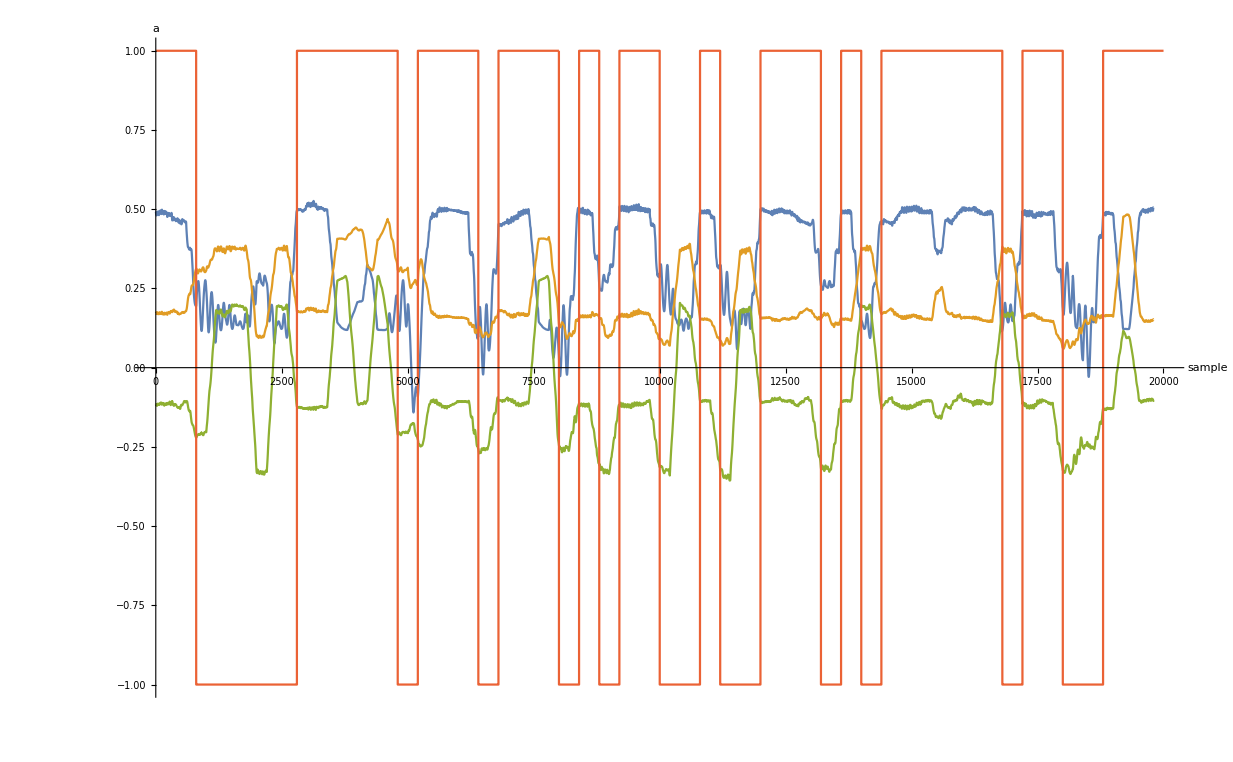

```mathematica
ListLinePlot[acceleration,{TargetUnits->{"sample","a"},AxesLabel->Automatic,PlotRange->{-1,1}}]
```

Suppose there are gaps

```mathematica
Manipulate[
start=7500;
sampleCount=1000;
gapLength=50;
axis=1;

data=acceleration[[axis]][[start;;start+sampleCount+gapLength]];
tsModelLength=100;
beforeGap=data[[gapStart-tsModelLength;;gapStart]];
beforeGapTD=TemporalData[beforeGap,{Range[tsModelLength+1]+gapStart-tsModelLength}];
proc=EstimatedProcess[beforeGap,ARProcess[50]];
tsmod=TimeSeriesModelFit[beforeGapTD,proc];
forecast=TimeSeriesForecast[tsmod,{gapLength}];
gapTD=TemporalData[ConstantArray[1,gapLength],{Range[gapLength]+gapStart}];
gapStart
ListLinePlot[{data,forecast,beforeGapTD,gapTD},Filling->{2->{1},3->{1},4->Bottom},PlotLegends->{"measured","forecast","training","gap"},TargetUnits->{"sample","a"},AxesLabel->Automatic,PlotRange->{-1,1},PlotStyle->{Blue,Orange,Green,Red}],
{gapStart,101,950}]
```